### plot style

```mathematica
SetOptions[{Plot, ListPlot, ListLinePlot, ListLogPlot, ListLogLogPlot}, {BaseStyle -> {FontFamily -> "Times", FontSize -> 18}, PlotStyle -> ColorData[108, "ColorList"], PlotRange -> All, Frame -> True, FrameLabel -> {"R (a_0)", "E (GHz × h)"}, GridLines -> Automatic, PlotLegends -> "Expressions", ImageSize -> Medium}];
```

## ulrm hybridized orbitals

## Setup

### Atomic Units Conversion

#### Boltzmann constant [T/J]

```mathematica
kB = 1.380649*10^(-23);
```

#### Bohr unit of length [m]

```mathematica
a0 = 5.29177210903*10^(-11);
```

#### time [s]

```mathematica
ts = 2.4188843265857*10^(-17);
```

#### velocity [m/s]

```mathematica
vms = 2.18769126364*10^6; (* =a0/ts *)
```

#### electron mass [kg]

```mathematica
me = 9.1093837015*10^(-31);
```

#### atomic mass in units of electron mass

```mathematica
M = 86.909180527*1822.888486192;(* atomic mass *)
```

#### temperatures from nK to K

```mathematica
T = Table[10^t, {t,-9,0,1}];
```

#### corresponding velocities in atomic units

```mathematica
vs = Sqrt[3 kB T/(M me)]/vms;
```

### Wavefunctions

#### Energies are displayed GHz

```mathematica
unit = 2 3.289841960355 10^6;
```

#### Radial hydrogenic wave function

```mathematica
U[n_,l_,r_] := Sqrt[(2/n)^3 ((n-l-1)!/(2n(n+l)!))] Exp[-r/n] (2(r/n))^l LaguerreL[n-l-1,2l+1,2(r/n)]
dU[n_,l_,r_] := D[x U[n,l,x],x] /. x->r
```

#### Radial quantum defect state wave function

```mathematica
W[n_,l_,r_] := 1/n/Sqrt[(n+l)! (n-l-1)!] WhittakerW[n,l+1/2,2r/n]/r
dW[n_,l_,r_] := D[x W[n,l,x],x] /. x->r
```

#### Angular wave function

```mathematica
Y[l_] := Sqrt[(2l+1)/(4π)]
Z[l_] := Sqrt[(2l+1)(l+1)l/(8π)]
```

#### Quantum defects for Rubidium

```mathematica
δRb = {3.1311804,2.65,1.34,0.0165192};
δ[l_]=If[l<Length[δRb],δRb[[l+1]],0];
```

#### Semi-classical electron wave number

```mathematica
kin[r_, n_] = Re[Sqrt[2(-(2n^2)^(-1) + 1/r)]];
```

#### Import s - wave scattering data

```mathematica
As = Interpolation[Import["/home/frederic/Documents/Wolfram Mathematica/data/Rbscat.csv", "Data"][[All,{1,2}]]];
```

#### Import p - wave scattering data

```mathematica
ApMod = Import["/home/frederic/Documents/Wolfram Mathematica/data/Rbscat.csv", "Data"][[All,{1,3}]];
cut = 224;
ApMod[[1;;cut,2]] = Table[ApMod[[cut,2]], {i,cut}];
Ap = Interpolation[ApMod];
```

#### Matrix elements for quantum defect wave functions

```mathematica
QΣ[n_, l_, r_] := With[{ν=n-FractionalPart[δ[l]]}, 2π Y[l]^2 (As[kin[r, n]] W[ν, l, r]^2 + 3 Ap[kin[r, n]] dW[ν, l, r]^2/r^2)]
QΠ[n_, l_, r_] := With[{ν=n-FractionalPart[δ[l]]}, 6π Z[l]^2 Ap[kin[r, n]] W[ν, l, r]^2/r^2]
```

#### Matrix element for the trilobite

Approximate formulation for fractional n (neglecting quantum defect states)

```mathematica
TrilU[n_, r_] := 2π As[kin[r, n]] (r(2n^2-r)(U[n,0,r]/n)^2+dU[n,0,r]^2)/(4π)
TrilW[n_, r_] := 2π As[kin[r, n]] (r(2n^2-r)(W[n,0,r]/n)^2+dW[n,0,r]^2)/(4π)
Trilobite[n_, r_] := If[n∈Integers, TrilU[n,r], TrilW[n,r]]
```

Exact formulation for integer n

```mathematica
Tril[n_, r_] := 2π As[kin[r, n]]Sum[U[n,l,r]^2 Y[l]^2,{l,4,n-1}]
```

Difference of the two formulations

```mathematica
TrilCorr[n_, r_] := 2π As[kin[r, n]]Sum[U[n,l,r]^2 Y[l]^2,{l,0,3}]
```

#### Matrix element for the butterfly

Approximate formulation for fractional n (neglecting quantum defect states)

```mathematica
ButterUθ[n_, r_] := 6π Ap[kin[r, n]] (r(2n^2-r)(r(2n^2-r)(U[n,0,r]/n)^2+dU[n,0,r]^2)/n^2-U[n,0,r] dU[n,0,r] r)/(12π r^2)
ButterWθ[n_, r_] := 6π Ap[kin[r, n]] (r(2n^2-r)(r(2n^2-r)(U[n,0,r]/n)^2+dW[n,0,r]^2)/n^2-W[n,0,r] dW[n,0,r] r)/(12π r^2)
Butterflyθ[n_, r_] := If[n∈Integers, ButterUθ[n,r], ButterWθ[n,r]]
```

```mathematica
ButterUR[n_, r_] := ButterUθ[n,r]-6π Ap[kin[r, n]] (2U[n,0,r]+3dU[n,0,r]) U[n,0,r]/r/(12π)
ButterWR[n_, r_] := ButterWθ[n,r]-6π Ap[kin[r, n]] (2W[n,0,r]+3dW[n,0,r]) W[n,0,r]/r/(12π)
ButterflyR[n_, r_] := If[n∈Integers, ButterUR[n,r], ButterWR[n,r]]
```

Exact formulation for integer n

```mathematica
Butterθ[n_, r_] := 6π Ap[kin[r, n]]Sum[U[n,l,r]^2/r^2 Z[l]^2,{l,4,n-1}]
ButterR[n_, r_] := 6π Ap[kin[r, n]] Sum[dU[n,l,r]^2/r^2 Y[l]^2,{l,4,n-1}]
```

Difference of the two formulations

```mathematica
ButterθCorr[n_, r_] := 6π Ap[kin[r, n]]Sum[U[n,l,r]^2/r^2 Z[l]^2,{l,0,3}]
ButterRCorr[n_, r_] := 6π Ap[kin[r, n]]Sum[dU[n,l,r]^2/r^2 Y[l]^2,{l,0,3}]
```

## Electronic potentials

### Parameters

```mathematica
n0 = 30;
R = Subdivide[0.4n0^2,2.4n0^2,400];
```

### Comparison of high -l PEC

#### phase shifts

```mathematica
δs[k_] := ArcTan[-k As[k]]
δp[k_] := With[{δ=ArcTan[-k^3 Ap[k]]}, If[δ<0,δ+π,δ]]
```

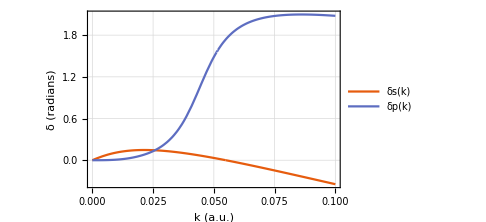

```mathematica
Plot[{δs[k],δp[k]},{k,0,0.1}, FrameLabel->{"k (a.u.)", "δ (radians)"}]
```

#### Borodin-Kazansky potentials

```mathematica
Es = Table[With[{δ=δs[kin[r,n0]]},1/(2n0^2)-1/(2(n0-δ/π)^2)],{r,R}];
Ep = Table[With[{δ=δp[kin[r,n0]]},1/(2n0^2)-1/(2(n0-δ/π)^2)],{r,R}];
```

```mathematica
Et = Table[Tril[n0,r],{r,R}]; // Timing
Eu = Table[TrilU[n0,r],{r,R}]; // Timing
Ev = Table[TrilU[n0,r]-TrilCorr[n0,r],{r,R}]; // Timing
```

{1.30272,Null}

{0.960426,Null}

{1.46985,Null}

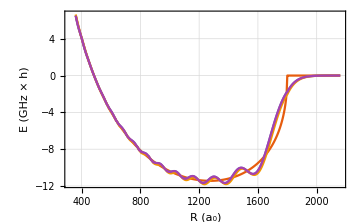

```mathematica
ListLinePlot[{{R,Es unit}ᵀ,{R,Et unit}ᵀ,{R,Eu unit}ᵀ,{R,Ev unit}ᵀ}]
```

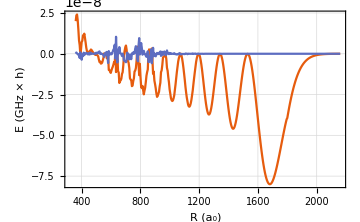

```mathematica
ListLinePlot[{{R,Eu-Et}ᵀ,{R,Et-Ev}ᵀ}]
```

```mathematica
Eb = Table[ButterR[n0,r],{r,R}]; // Timing
Ec = Table[ButterUR[n0,r],{r,R}]; // Timing
Ed = Table[ButterUR[n0,r]-ButterRCorr[n0,r],{r,R}]; // Timing
```

{6.75339,Null}

{1.45141,Null}

{2.97554,Null}

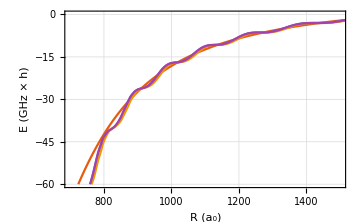

```mathematica
ListLinePlot[{{R,Ep unit}ᵀ,{R,Eb unit}ᵀ,{R,Ec unit}ᵀ,{R,Ed unit}ᵀ}, PlotRange->{{700,1500},{-60,0}}]
```

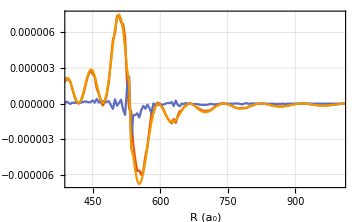

```mathematica
ListLinePlot[{{R,Ec-Eb}ᵀ,{R,Eb-Ed}ᵀ,{R,Ec-Ed}ᵀ}, PlotRange->{{400,1000},Full}]
```

```mathematica
Ee = Table[Butterθ[n0,r],{r,R}]; // Timing
Ef = Table[ButterUθ[n0,r],{r,R}]; // Timing
Eg = Table[ButterUθ[n0,r]-ButterθCorr[n0,r],{r,R}]; // Timing
```

{1.25102,Null}

{0.882275,Null}

{1.06183,Null}

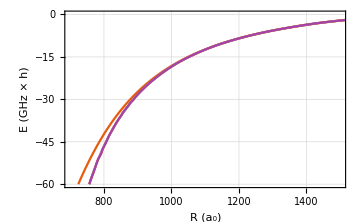

```mathematica
ListLinePlot[{{R,Ep unit}ᵀ,{R,Ee unit}ᵀ,{R,Ef unit}ᵀ,{R,Eg unit}ᵀ}, PlotRange->{{700,1500},{-60,0}}]
```

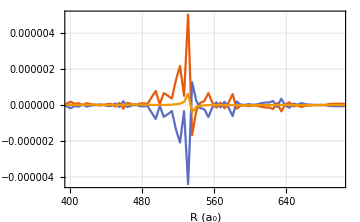

```mathematica
ListLinePlot[{{R,Ef-Ee}ᵀ,{R,Ee-Eg}ᵀ,{R,Ef-Eg}ᵀ}, PlotRange->{{400,700},Full}]
```

### low - l PEC

```mathematica
EΣs=Table[QΣ[n0,0,r],{r,R}]; // Timing
EΣp=Table[QΣ[n0,1,r],{r,R}]; // Timing
EΣd=Table[QΣ[n0,2,r],{r,R}]; // Timing
EΣf=Table[QΣ[n0,3,r],{r,R}]; // Timing
```

{1.89583,Null}

{1.71499,Null}

{1.61578,Null}

{1.483,Null}

```mathematica
EΠs=Table[QΠ[n0,0,r],{r,R}]; // Timing
EΠp=Table[QΠ[n0,1,r],{r,R}]; // Timing
EΠd=Table[QΠ[n0,2,r],{r,R}]; // Timing
EΠf=Table[QΠ[n0,3,r],{r,R}]; // Timing
```

{0.485422,Null}

{0.525832,Null}

{0.52772,Null}

{0.506857,Null}

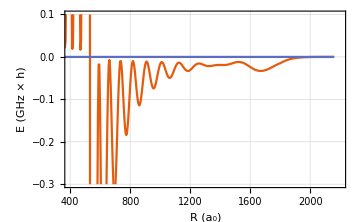

```mathematica
ListLinePlot[{{R,EΣs unit}ᵀ,{R,EΠs unit}ᵀ}, PlotRange->{{400,2200},{-0.3,0.1}}]
```

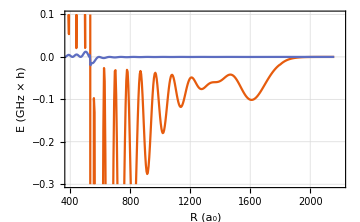

```mathematica
ListLinePlot[{{R,EΣp unit}ᵀ,{R,EΠp unit}ᵀ}, PlotRange->{{400,2200},{-0.3,0.1}}]
```

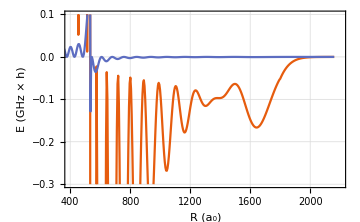

```mathematica
ListLinePlot[{{R,EΣd unit}ᵀ,{R,EΠd unit}ᵀ}, PlotRange->{{400,2200},{-0.3,0.1}}]
```

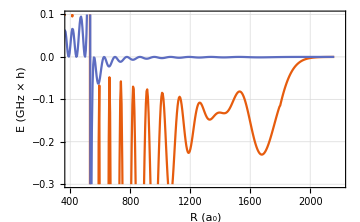

```mathematica
ListLinePlot[{{R,EΣf unit}ᵀ,{R,EΠf unit}ᵀ}, PlotRange->{{400,2200},{-0.3,0.1}}]
```